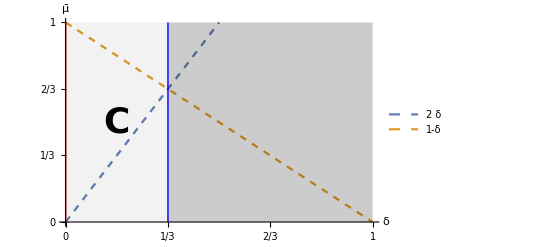

```mathematica
With[{fontSize=18},Plot[{2δ,1-δ},{δ,0,1},PlotRange->{{0,1}},PlotLegends->Placed[LineLegend["Expressions",LabelStyle->fontSize],{Right,Center}],PlotStyle->Dashed,Ticks->{{0,1/3,2/3,1}},AxesLabel->{Automatic,OverBar[μ]},AxesStyle->Directive[Black,fontSize],Epilog->{Opacity[0.05],Polygon[{{1/3,0},{1/3,1},{0,1},{0,0}}],Opacity[0.2],Polygon[{{1/3,0},{1/3,1},{1,1},{1,0}}],Opacity[1],Text[Style["C",2fontSize,Bold],{1/6,1/2}],Thick,Red,Line[{{0,0},{0,1}}],Blue,Line[{{1/3,0},{1/3,1}}]}]]
```